```mathematica
a[n_]= If[n==1,7,1+(1/(3*a[n-1]))]
```

If[n==1,7,1+1/(3 a[n-1])]

```mathematica
If[n==1,7,1+1/(3 a[n-1])]
```

If[n==1,7,1+1/(3 a[n-1])]

```mathematica
a[1]
```

7

```mathematica
a[2]
```

22/21

```mathematica
N[a[10],11]
```

1.2637617093

```mathematica
N[Table[a[n],{n,2,30}]]
```

{1.04762,1.31818,1.25287,1.26606,1.26329,1.26386,1.26374,1.26377,1.26376,1.26376,1.26376,1.26376,1.26376,1.26376,1.26376,1.26376,1.26376,1.26376,1.26376,1.26376,1.26376,1.26376,1.26376,1.26376,1.26376,1.26376,1.26376,1.26376,1.26376}

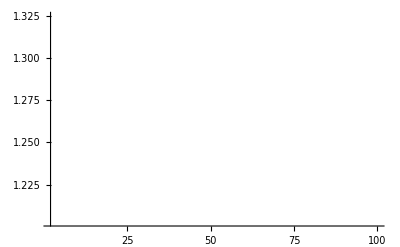

```mathematica
DiscretePlot[If[n==1,7,1+1/(3 a[n-1])],{n,2,100}]
```

```mathematica
NSolve[x==1+(1/(3*x)),x]
```

{{x→1.26376},{x→-0.263763}}

```mathematica
b[n_]=If[n==1,2,Sqrt[5+4*b[n-1]]]
```

If[n==1,2,√(5+4 b[n-1])]

```mathematica
b[1]
```

2

```mathematica
b[2]
```

√13

```mathematica
N[b[15],21]
```

4.99998963517891099943

```mathematica
Table[N[b[n],20],{n,1,30}]
```

{2.,3.6055512754639892931,4.407063092565836772,4.7569162668963752833,4.9018022264862442258,4.9605653816823115131,4.9842011924408956439,4.9936764782836685661,4.9974699511987737678,4.9989878780404234014,4.9995951348245883344,4.9998380513070974205,4.9999352201031954652,4.9999740879741348776,4.9999896351789109994,4.9999958540698455261,4.9999983416276631906,4.999999336651021273,4.9999997346604014687,4.999999893864159461,4.9999999575456636042,4.9999999830182654128,4.9999999932073061605,4.9999999972829224635,4.9999999989131689853,4.9999999995652675941,4.9999999998261070376,4.9999999999304428151,4.999999999972177126,4.9999999999888708504}

Clear

```mathematica
RSolve[{d[n]==2*d[n-1]+1,d[1]==1},d[n],n]
```

{{d[n]→-1+2^n}}

```mathematica
f[n_]=If[n==2,-3,f[n-1]/5+n^2-1]
```

If[n==2,-3,1/5 f[n-1]+n^2-1]

```mathematica
N[f[12]]
```

171.719

```mathematica
N[f[100]]
```

12436.7

```mathematica
Clear[f]
```

```mathematica
RSolve[{f[2]==-3,f[n+1]==f[n]/5+n^2-1},f[n],n]
```

{{f[n]→1/32 5^(1-n) (-455+7 5^n-4 5^(1+n) n+8 5^n n^2)}}

```mathematica
Clear[a]
```

```mathematica
RSolve[{a[0]==3,a[1]==-2,a[n+2]==6a[n+1]-9a[n]+5n},a[n],n]
```

{{a[n]→1/4 (5+7 3^n+5 n-13 3^n n)}}

```mathematica
Clear[a]
```

```mathematica
RSolve[{a[n+3]-3a[n+2]-a[n+1]+3a[n]==2^n},a[n],n]
```

{{a[n]→-2^n/3+(-1)^n C[1]+C[2]+3^n C[3]}}